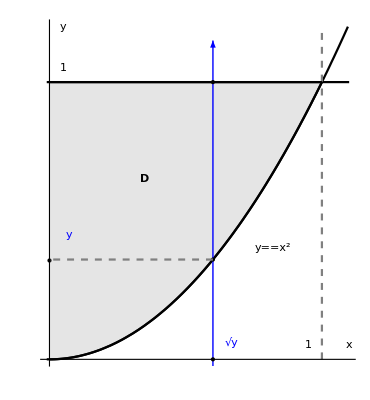

```mathematica
f1=Plot[{1,x^2},{x,0,1},
AspectRatio->Automatic,
Filling->{2->{1}},
FillingStyle->{Gray,Opacity[0.7]},
PlotStyle->{{Black},{Black}}
];
f2=ContourPlot[{y==1,y==x^2,x==1},{x,-0.01,1.1},{y,0,1.2},
AspectRatio->Automatic,
Axes->True,AxesOrigin->{0,0},
(*AxesLabel->{x,y}, *)
AxesStyle->Arrowheads[0.03],
Frame->False,
Ticks->None,
(*Ticks->{{0,1},{1}},TicksStyle->Directive[Black, 14],*)
ContourStyle->{{Black},{Black},{Gray,Dashed}}
];
(********彩色箭头*******)
(*f3=Plot[0.4,{x,-0.2,0.8},PlotStyle->Arrowheads[0.03]];*)
(*f3=Graphics[{Red,Arrowheads[0.03],Arrow[{{-0.2,0.4},{0.8,0.4}}]}];*)
f3=Graphics[{Blue,Arrowheads[0.03],Arrow[{{0.6,-0.1},{0.6,1.15}}]}];
(*********入射、出射点********)
(*f4=Graphics[{{PointSize[Large],Point[{0,0.4}]},{PointSize[Large],Point[{2*Sqrt[0.1],0.4}]}}];*)
f4=Graphics[{{PointSize[Large],Point[{0.6,0.36}]},
{PointSize[Large],Point[{0.6,1}]},
{PointSize[Large],Point[{0.6,0}]},
{PointSize[Large],Point[{0,0.36}]}
}];
(*********虚线*********)
(*f5=ContourPlot[x==2*Sqrt[0.1],{x,0,1},{y,0,0.4},
ContourStyle->{Gray,Dashed}];*)
f5=ContourPlot[y==0.36,{x,0,0.6},{y,0,0.4},
ContourStyle->{Gray,Dashed}];
(*********文字标记*********)
f6=Graphics[{Text[Style["y",Large,Italic],{0.05,1.2}],
Text[Style["x",Large,Italic],{1.1,0.05}],
Text[Style["D",Large,Black,Bold,Italic],{0.35,0.65}],
Text[Style["y"==x^2,Large,Italic],{0.82,0.4}],
(*Text[Style["y"==Sqrt[x],Medium,Italic],{0.75,0.2}]*)
Text[Style[Sqrt["y"],Blue,Large,Italic],{0.67,0.06}],
Text[Style["y",Blue,Large,Italic],{0.07,0.45}],
Text[Style[1,Large,Italic],{0.05,1.05}],
Text[Style[1,Large,Italic],{0.95,0.05}]
}];
(*********选择显示*********)
Show[f2,f1,f3,f4,f5,f6]
```

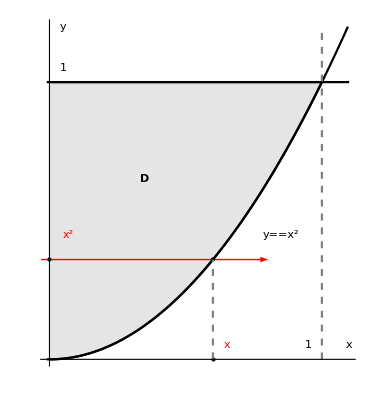

```mathematica
f1=Plot[{1,x^2},{x,0,1},
AspectRatio->Automatic,
Filling->{2->{1}},
FillingStyle->{Gray,Opacity[0.7]},
PlotStyle->{{Black},{Black}}
];
f2=ContourPlot[{y==1,y==x^2,x==1},{x,-0.01,1.1},{y,0,1.2},
AspectRatio->Automatic,
Axes->True,AxesOrigin->{0,0},
(*AxesLabel->{x,y}, *)
AxesStyle->Arrowheads[0.03],
Frame->False,
Ticks->None,
(*Ticks->{{0,1},{1}},TicksStyle->Directive[Black, 14],*)
ContourStyle->{{Black},{Black},{Gray,Dashed}}
];
(********彩色箭头*******)
f3=Graphics[{Red,Arrowheads[0.03],Arrow[{{-0.2,0.36},{0.8,0.36}}]}];
(*********入射、出射点********)
f4=Graphics[{{PointSize[Large],Point[{0.6,0.36}]},
{PointSize[Large],Point[{0.6,0}]},
{PointSize[Large],Point[{0,0.36}]}
}];
(*********虚线*********)
f5=ContourPlot[x==0.6,{x,0,1},{y,0,0.36},
ContourStyle->{Gray,Dashed}];
(*********文字标记*********)
f6=Graphics[{Text[Style["y",Large,Italic],{0.05,1.2}],
Text[Style["x",Large,Italic],{1.1,0.05}],
Text[Style["D",Large,Black,Bold,Italic],{0.35,0.65}],
Text[Style["y"==x^2,Large,Italic],{0.85,0.45}],
(*Text[Style["y"==Sqrt[x],Medium,Italic],{0.75,0.2}]*)
Text[Style[x,Red,Large,Italic],{0.65,0.05}],
Text[Style[x^2,Red,Large,Italic],{0.07,0.45}],
Text[Style[1,Large,Italic],{0.05,1.05}],
Text[Style[1,Large,Italic],{0.95,0.05}]
}];
(*********选择显示*********)
Show[f2,f1,f3,f4,f5,f6]
```

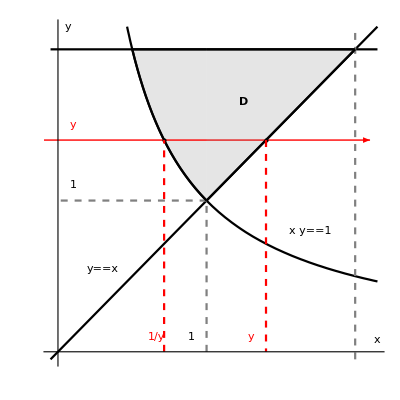

```mathematica
(********区域*******)
f1=Plot[{2,1/x},{x,1/2,1},
Filling->{2->{1}},
FillingStyle->{Gray,Opacity[0.7]},
PlotStyle->{{Black},{Black}}
];
f12=Plot[{2,x},{x,1,2},
Filling->{2->{1}},
FillingStyle->{Gray,Opacity[0.7]},
PlotStyle->{{Black},{Black}}
];
(********函数*******)
f2=ContourPlot[{y==2,x*y==1,y==x,x==2},{x,-0.05,2.15},{y,-0.05,2.15},
AspectRatio->Automatic,
Axes->True,AxesOrigin->{0,0},
(*AxesLabel->{x,y}, *)
AxesStyle->Arrowheads[0.03],
Frame->False,
Ticks->None,
(*Ticks->{{0,1},{1}},TicksStyle->Directive[Black, 14],*)
ContourStyle->{{Black},{Black},{Black},{Gray,Dashed}}
];
(********彩色箭头*******)
f3=Graphics[{Red,Arrowheads[0.03],Arrow[{{-0.2,1.4},{2.1,1.4}}]}];
(*********入射、出射点********)
f4=Graphics[{
(*{PointSize[Large],Point[{0,1.4}]},*)
{PointSize[Large],Point[{1/1.4,1.4}]},
{PointSize[Large],Point[{1.4,1.4}]}
}];
(*********虚线*********)
f5=ContourPlot[x==1,{x,0,2},{y,0,1},
ContourStyle->{Gray,Dashed}];
f51=ContourPlot[y==1,{x,0,1},{y,0,2},
ContourStyle->{Gray,Dashed}];
f52=ContourPlot[x==1/1.4,{x,0,2},{y,0,1.4},
ContourStyle->{Red,Dashed}];
f53=ContourPlot[x==1.4,{x,0,2},{y,0,1.4},
ContourStyle->{Red,Dashed}];
(*********文字标记*********)
f6=Graphics[{Text[Style["y",Large,Italic],{0.07,2.15}],
Text[Style["x",Large,Italic],{2.15,0.08}],
Text[Style["D",Large,Black,Bold,Italic],{1.25,1.65}],
Text[Style["y"==x,Large,Italic],{0.3,0.55}],
Text[Style[x"y"==1,Large,Italic],{1.7,0.8}],
(*Text[Style["y"==Sqrt[x],Medium,Italic],{0.75,0.2}]*)
Text[Style["y",Red,Large,Italic],{0.1,1.5}],
Text[Style[1/"y",Red,Medium,Italic],{1/1.4-0.05,0.1}],
Text[Style["y",Red,Large,Italic],{1.3,0.1}],
Text[Style[1,Large,Italic],{0.1,1.1}],
Text[Style[1,Large,Italic],{0.9,0.1}]
}];
(*********选择显示*********)
Show[f2,f1,f3,f12,f4,f5,f51,f52,f53,f6]
```

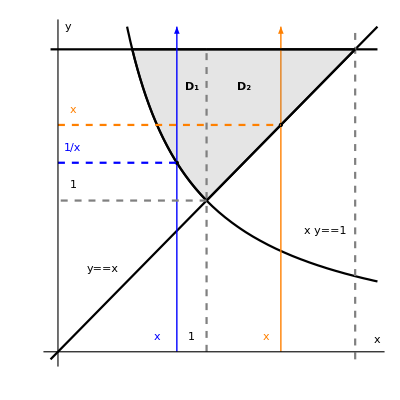

```mathematica
(********区域*******)
f1=Plot[{2,1/x},{x,1/2,1},
Filling->{2->{1}},
FillingStyle->{Gray,Opacity[0.7]},
PlotStyle->{{Black},{Black}}
];
f12=Plot[{2,x},{x,1,2},
Filling->{2->{1}},
FillingStyle->{Gray,Opacity[0.7]},
PlotStyle->{{Black},{Black}}
];
(********函数*******)
f2=ContourPlot[{y==2,x*y==1,y==x,x==2},{x,-0.05,2.15},{y,-0.05,2.15},
AspectRatio->Automatic,
Axes->True,AxesOrigin->{0,0},
(*AxesLabel->{x,y}, *)
AxesStyle->Arrowheads[0.03],
Frame->False,
Ticks->None,
(*Ticks->{{0,1},{1}},TicksStyle->Directive[Black, 14],*)
ContourStyle->{{Black},{Black},{Black},{Gray,Dashed}}
];
(********彩色箭头*******)
f3=Graphics[{Blue,Arrowheads[0.03],Arrow[{{0.8,0},{0.8,2.15}}]}];
f31=Graphics[{Orange,Arrowheads[0.03],Arrow[{{1.5,0},{1.5,2.15}}]}];
(*********入射、出射点********)
f4=Graphics[{
(*{PointSize[Large],Point[{0,1.4}]},*)
{PointSize[Large],Point[{0.8,1/0.8}]},
{PointSize[Large],Point[{1.5,1.5}]}
}];
(*********虚线*********)
f5=ContourPlot[x==1,{x,0,2},{y,0,2},
ContourStyle->{Gray,Dashed}];
f51=ContourPlot[y==1,{x,0,1},{y,0,2},
ContourStyle->{Gray,Dashed}];
f52=ContourPlot[y==1/0.8,{x,0,0.8},{y,0,2},
ContourStyle->{Blue,Dashed}];
f53=ContourPlot[y==1.5,{x,0,1.5},{y,0,2},
ContourStyle->{Orange,Dashed}];
(*********文字标记*********)
f6=Graphics[{Text[Style["y",Large,Italic],{0.07,2.15}],
Text[Style["x",Large,Italic],{2.15,0.08}],
Text[Style[Subscript[D, 1],Large,Black,Bold,Italic],{0.9,1.75}],
Text[Style[Subscript[D, 2],Large,Black,Bold,Italic],{1.25,1.75}],
Text[Style["y"==x,Large,Italic],{0.3,0.55}],
Text[Style[x"y"==1,Large,Italic],{1.8,0.8}],
(*Text[Style["y"==Sqrt[x],Medium,Italic],{0.75,0.2}]*)
Text[Style[x,Orange,Large,Italic],{0.1,1.6}],
Text[Style[x,Blue,Large,Italic],{1/1.4-0.05,0.1}],
Text[Style[1/x,Blue,Medium,Italic],{0.1,1/0.8+0.1}],
Text[Style[x,Orange,Large,Italic],{1.4,0.1}],
Text[Style[1,Large,Italic],{0.1,1.1}],
Text[Style[1,Large,Italic],{0.9,0.1}]
}];
(*********选择显示*********)
Show[f2,f1,f3,f31,f12,f4,f5,f51,f52,f53,f6]
```